```mathematica
(*Strictly square grid lattice *)
ClearAll["Global`*"];Clear[Derivative];
```

```mathematica
SetDirectory["/Users/tosku/Documents/sggs/"]
```

/Users/tosku/Documents/sggs

```mathematica
Import[NotebookDirectory[]<>"lattice.wl"];
```

```mathematica
L=5;
d:=2;
```

```mathematica
(*lattice=getFreeBoundaryLattice[L,d];*)
latticeFile="tests/L5/1.lattice";
OpenRead[latticeFile];
ledgelist=ReadList[latticeFile, {Number,Number,Number}];
Close[latticeFile];
lattice=Graph[listToEdges[{#[[1]],#[[2]]}&/@ledgelist],EdgeWeight->First[{Last[#]&/@ledgelist}]];
```

```mathematica
(*Function to map Plaquettes as lists of edges *)
nV[i_,j_,L_]:=nextVertexFreeBoundary[i,j,L];
pV[i_,j_,L_]:=previousVertexFreeBoundary[i,j,L];
plaquetteOfVertexInPlane[i_,plane_,L_]:=
Fold[If[#1=={},
Append[#1,{i,nV[i,#2,L]}],
If[NumericQ[Last[Last[#1]]],
Append[#1,{Last[Last[#1]],
If[Length[#1]<2,
nV[Last[Last[#1]],#2,L],
pV[Last[Last[#1]],#2,L]
]}
],Append[#1,{Last[Last[#1]],False}]]
]&,{},Join[plane,plane]]
```

```mathematica
isPlaquette[plaquette_]:=Fold[If[#1==True&&NumericQ[First[#2]]&&NumericQ[Last[#2]],True,False]&,True,plaquette]
```

```mathematica
getInternalPlaquettes[L_,d_]:=Select[Sort[Flatten[Map[Function[vl,plaquetteOfVertexInPlane[vl,#,L]&/@Subsets[Range[1,d],{2}]][#]&,Range[1,L^d]],1]],isPlaquette];
```

```mathematica
(*get the bottom left vertex of a plaquette*)
getVertexOfPlaquette[plaq_]:=Min[Flatten[plaq]];
```

```mathematica
isFrustrated[graph_,cycle_]:= Fold[#1*Jij[graph, Apply[UndirectedEdge,#2]]&,1,cycle]<0;
```

```mathematica
totalFrustration[graph_,cycles_]:=Length[Select[cycles,isFrustrated[graph,#]&]];
totalFrustration[lattice,getInternalPlaquettes[L,d]];N[totalFrustration[lattice,getInternalPlaquettes[L,d]]/Length[getInternalPlaquettes[L,d]]]
```

0.5

```mathematica
(* skewed city as edge lists *)
getSkewedCity[label_]:={{Append[label,1],Append[label,2]},{Append[label,2],Append[label,5]},{Append[label,5],Append[label,3]},{Append[label,3],Append[label,4]},{Append[label,4],Append[label,6]},{Append[label,6],Append[label,1]},{Append[label,5],Append[label,6]}}
```

```mathematica
getKasteleynCity[label_]:={{Append[label,1],Append[label,2]},{Append[label,2],Append[label,3]},{Append[label,3],Append[label,4]},{Append[label,1],Append[label,3]},{Append[label,2],Append[label,4]},{Append[label,4],Append[label,1]}}
```

```mathematica
buildInnerSkewedCities[L_,d_]:=getSkewedCity[{getVertexOfPlaquette[#]}]&/@getInternalPlaquettes[L,d]

(*buildBorderSkewedCities[L_,d_]:=Fold[Append[#1,getSkewedCity[{L^2+#2}]]&,{},Range[1,4*L]]*)

buildBorderSkewedCities[L_,d_]:=Fold[Append[#1,getKasteleynCity[{L^2+#2}]]&,{},Range[1,4*L]]

(*sides like directions are 1 right, 2 up, 3 left, 4, down *)
(*buildBorderIntraEdges[L_,d_]:=Flatten[Fold[
Append[#1,{{{#2,2},{#2+1,4}},
{{#2,1},{#2+2(L-1),3}},
{{#2+L-1,1},{#2+L,3}},
{{#2+L-1,2},{#2+3(L-1),4}},
{{#2+2(L-1),2},{#2+2(L-1)+1,4}},
{{#2+3(L-1),1},{#2+3(L-1)+1,3}}
}]&,{},Range[L^2+1,L^2+L-2]],1]

cornerDualEdges[L_]:=Flatten[Fold[Append[#1,
If[#2==1,{{{L^2+4L-4+#2,4},{L^2+L-1,2}},
{{L^2+4L-4+#2,3},{L^2+2(L-1),1}}
,{{L^2+4L-4+#2,2},{L^2+4L-4+2,4}},
{{L^2+4L-4+#2,1},{L^2+4L-4+3,3}}
},
If[#2==2,{{{L^2+4L-4+#2,2},{L^2+1,4}},{{L^2+4L-4+#2,3},{L^2+4(L-1),1}}},
If[#2==3,{{{L^2+4L-4+#2,1},{L^2+L,3}},{{L^2+4L-4+#2,4},{L^2+3(L-1),2}}},
{{{L^2+4L-4+#2,2},{L^2+2(L-1)+1,4}},
{{L^2+4L-4+#2,1},{L^2+3(L-1)+1,3}}
,{{L^2+4L-4+#2,3},{L^2+4L-4+2,1}},
{{L^2+4L-4+#2,4},{L^2+4L-4+3,2}}
}]
]
]
]&,{},Range[1,4]],1]*)

buildBorderIntraEdges[L_,d_]:=Flatten[Fold[
Append[#1,{{{#2,2},{#2+1,4}},
(*{{#2,1},{#2+2(L-1),3}},*)
{{#2+L-1,1},{#2+L,3}},
(*{{#2+L-1,2},{#2+3(L-1),4}},*)
{{#2+2(L-1),2},{#2+2(L-1)+1,4}},
{{#2+3(L-1),1},{#2+3(L-1)+1,3}}
}]&,{},Range[L^2+1,L^2+L-2]],1]

cornerDualEdges[L_]:=Flatten[Fold[Append[#1,
If[#2==1,{{{L^2+4L-4+#2,4},{L^2+L-1,2}},
{{L^2+4L-4+#2,3},{L^2+2(L-1),1}}
(*,{{L^2+4L-4+#2,2},{L^2+4L-4+2,4}},
{{L^2+4L-4+#2,1},{L^2+4L-4+3,3}}*)
},
If[#2==2,{{{L^2+4L-4+#2,2},{L^2+1,4}},{{L^2+4L-4+#2,3},{L^2+4(L-1),1}}},
If[#2==3,{{{L^2+4L-4+#2,1},{L^2+L,3}},{{L^2+4L-4+#2,4},{L^2+3(L-1),2}}},
{{{L^2+4L-4+#2,2},{L^2+2(L-1)+1,4}},
{{L^2+4L-4+#2,1},{L^2+3(L-1)+1,3}}
(*,{{L^2+4L-4+#2,3},{L^2+4L-4+2,1}},
{{L^2+4L-4+#2,4},{L^2+4L-4+3,2}}*)
}]
]
]
]&,{},Range[1,4]],1]
```

```mathematica
GEdgeToDEdgeInternal[gedge_,L_,d_]:=If[getEdgeDirection[gedge,L,d]==1,
{{First[Sort[gedge]],4},{previousVertex[First[Sort[gedge]],2,L],2}},
{{First[Sort[gedge]],3},{previousVertex[First[Sort[gedge]],1,L],1}}
]
GEdgeToDEdgeBoundary[gedge_,L_,d_]:=If[getEdgeDirection[gedge,L,d]==2,
If[NumberQ[nextVertexFreeBoundary[First[gedge],1,L]],(*direction h=1*)
(*direction h=3*){{First[Sort[gedge]],3},{L^2+2(L-1)+(First[Sort[gedge]]+L-1)/L,1}},
{{previousVertex[First[Sort[gedge]],1,L],1},{L^2+(nextVertex[First[Sort[gedge]],1,L]+L-1)/L,3}}
],
If[NumberQ[nextVertexFreeBoundary[First[gedge],2,L]],(*direction h=2*)
(*direction h=4*){{First[Sort[gedge]],4},{L^2+3(L-1)+First[Sort[gedge]],2}},
{{previousVertex[First[Sort[gedge]],2,L],2},{L^2+(L-1)+nextVertex[First[Sort[gedge]],2,L],4}}
]	
]
(*1->2, 2->1, 3->2, 4->1*)
invertDirection[dir_]:=Mod[dir,2]+1;
GEdgeToDEdge[gedge_,L_,d_]:=If[isSurfaceEdge[gedge,L,d],
GEdgeToDEdgeBoundary[gedge,L,d],
GEdgeToDEdgeInternal[gedge,L,d]
]

getIntraCityDualEdges[lattice_,L_,d_]:=
listToEdges[Fold[Append[#1,GEdgeToDEdge[#2,L,d]]&,{}, EdgeList[lattice]]]

zeroWeights[graph_]:=Fold[SetProperty[{#1,#2},EdgeWeight->0]&,graph,EdgeList[graph]]

addWeights[dualgraph_,lattice_,L_,d_]:=Fold[SetProperty[{#1,listToEdges[{GEdgeToDEdge[edgesToList[#2],L,d]}]},EdgeWeight->Jij[lattice,#2]]&,zeroWeights[dualgraph],Apply[listToEdges,EdgeList[lattice]&]];
```

```mathematica
getDual[lattice_,L_,d_]:=Graph[Flatten[Join[
listToEdges[#]&/@Join[
buildInnerSkewedCities[L,d],buildBorderSkewedCities[L,d]
],getIntraCityDualEdges[lattice,L,d]
,listToEdges[buildBorderIntraEdges[L,d]]
,listToEdges[cornerDualEdges[L]]
],1] ]
dualGraph=addWeights[getDual[lattice,L,d],lattice,L,d];
BipartiteGraphQ[dualGraph]
```

False

```mathematica
relabelEdges[graph_]:={First[First[Position[VertexList[graph],First[#]]]]-1,First[First[Position[VertexList[graph],Last[#]]]]-1,PropertyValue[{graph,#},EdgeWeight]}&/@EdgeList[graph];
```

```mathematica
stringifyGraph[graph_]:=ToString[VertexCount[graph]]<>" "<>ToString[EdgeCount[graph]]<>"\n"<>Fold[If[#1==3,#2<>"\n",#1<>ToString[#2]<>"\n"]&,3,ToString[#[[1]]]<>" "<>ToString[#[[2]]]<>" "<>ToString[#[[3]]]&/@relabelEdges[graph]];
```

```mathematica
basename="~/Documents/sggs/"<>DateString["ISODateTime"]<>"_L"<>ToString[L]<>"_d"<>ToString[d];
```

```mathematica
st=OpenWrite[basename<>".matchdual"]
WriteString[st, stringifyGraph[dualGraph]]
Close[st]
```

OutputStream[…]

/Users/tosku/Documents/sggs/2016-08-24T18:51:17_L5_d2.matchdual

```mathematica
Run["blossom5/blossom5 -e "<>basename<>".matchdual -w "<>basename<>".matching"]
```

0

```mathematica
matchfile=OpenRead[basename<>".matching"]
NMatchedEdges=Drop[ReadList[matchfile, {Number,Number}],1];
Close[matchfile]
```

InputStream[…]

/Users/tosku/Documents/sggs/2016-08-24T18:51:17_L5_d2.matching

```mathematica
NMatched =Graph[listToEdges[NMatchedEdges]];
```

```mathematica
NM=Graph[UndirectedEdge[#[[1]],#[[2]]]&/@relabelEdges[dualGraph]];
```

```mathematica
NormalizedEdgeToDualEdge[NEdge_,dualGraph_]:={VertexList[dualGraph][[First[NEdge]+1]],VertexList[dualGraph][[Last[NEdge]+1]]};
```

```mathematica
Matched=NormalizedEdgeToDualEdge[#,dualGraph]&/@NMatchedEdges;
```

```mathematica
HighlightGraph[dualGraph,listToEdges[Matched],GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Show[SetProperty[%1409,VertexLabels->"Name"],PlotRange->All]
```

-Graphics-

```mathematica
Select[listToEdges[Matched],Jij[dualGraph,#]!=0&]//Sort//Length
Total[Jij[dualGraph,#]&/@listToEdges[Matched]]
```

16

-10

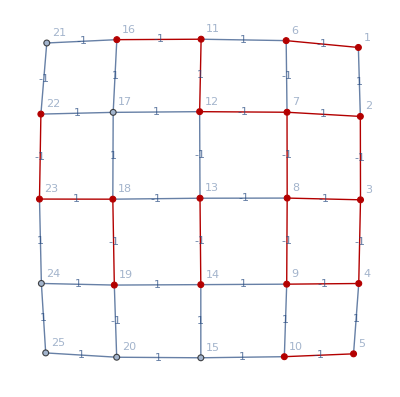

```mathematica
(*SortEdge beforhand*)
DEdgeToGEdge[dedge_,L_]:=If[First[Last[dedge]]<L^2,
{First[Last[dedge]],nextVertex[First[Last[dedge]],invertDirection[Last[Last[dedge]]],L]},
If[Last[First[dedge]]==1||Last[First[dedge]]==2,
{nextVertex[First[First[dedge]],Last[First[dedge]],L],nextVertex[nextVertex[First[First[dedge]],Last[First[dedge]],L],invertDirection[Last[Last[dedge]]],L]},
{First[First[dedge]],nextVertex[First[First[dedge]],invertDirection[Last[First[dedge]]],L]}
]
]
DualReversedEdgesToGraphEdges[reversedDualEdges_]:=DEdgeToGEdge[Sort[#],L]&/@reversedDualEdges
reversedGEdges = DualReversedEdgesToGraphEdges[Select[listToEdges[Matched],Jij[dualGraph,#]!=0&]];
HighlightGraph[lattice,Graph[listToEdges[reversedGEdges]]]//labelVertices//labelEdges
```

```mathematica
reversedEdgesToSpins[reversedEdges_,lattice_,i_]:=Fold[
If[Count[reversedEdges,{First[#2],Last[#2]}]==0&&Count[reversedEdges,{Last[#2],First[#2]}]==0,
If[Spin[First[#2],#1]==0,
ReplacePart[#1,First[#2]->Spin[Last[#2],#1]],
ReplacePart[#1,Last[#2]->Spin[First[#2],#1]]
],
If[Spin[First[#2],#1]==0,
ReplacePart[#1,First[#2]->-Spin[Last[#2],#1]],
ReplacePart[#1,Last[#2]->-Spin[First[#2],#1]]
]
]&,ReplacePart[ConstantArray[0,VertexCount[lattice]],i->1],edgesToList[Reap[DepthFirstScan[labelEdges[lattice],i,{"FrontierEdge"->Sow}]]⟦2,1⟧]];

GS=reversedEdgesToSpins[reversedGEdges,lattice,1]
Energy[lattice,reversedEdgesToSpins[reversedGEdges,lattice,#]]&/@VertexList[lattice]
```

{1,1,-1,1,1,-1,-1,1,-1,-1,-1,1,1,-1,-1,1,1,1,-1,-1,1,1,-1,-1,-1}

{-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20,-20}

```mathematica
TrueGS={1,1,1,-1,-1,-1,1,-1,1,1,-1,-1,1,1,1,-1,-1,-1,1,1,1,-1,1,1,1}
getUnsatisfiedEdgesFromSpins[spinConf_,lattice_]:=Fold[If[Spin[First[#2],spinConf]*Spin[Last[#2],spinConf]*Jij[lattice,#2]>0,#1,Append[#1,#2]]&,{},EdgeList[lattice]]
getUnsatisfiedEdgesFromSpins[TrueGS,lattice]
getReversedEdgesFromSpins[spinConf_,lattice_]:=Fold[If[Spin[First[#2],spinConf]*Spin[Last[#2],spinConf]>0,#1,Append[#1,#2]]&,{},EdgeList[lattice]]

reversedGEdges
Total[Jij[lattice,#]&/@listToEdges[reversedGEdges]]

getReversedEdgesFromSpins[TrueGS,lattice]
Total[Jij[lattice,edgesToList[#]]&/@getReversedEdgesFromSpins[TrueGS,lattice]]
Length[%]
```

{1,1,1,-1,-1,-1,1,-1,1,1,-1,-1,1,1,1,-1,-1,-1,1,1,1,-1,1,1,1}

{2<->3,11<->16,13<->14,18<->23,19<->20}

{{2,7},{1,6},{3,8},{7,8},{2,3},{4,9},{8,9},{3,4},{5,10},{7,12},{11,12},{13,14},{11,16},{18,19},{18,23},{22,23}}

-10

{1<->6,3<->4,3<->8,4<->9,5<->10,6<->7,7<->8,7<->12,8<->9,8<->13,12<->13,13<->18,16<->21,18<->19,18<->23,21<->22,22<->23}

-15

0